```mathematica
Remove["Global`*"]
(*Constants*)
```

```mathematica
c = 2.99792458*^8;
h = 6.62607004*^-34;
ℏ = h/(2π);
ϵo = 8.8541878128*^-12;
kb = 1.38064852*^-23;
e = 1.60217662*^-19;
a0 = 0.529177210903*^-10;
Be=.368;
ωe=700;
Ω=1;
```

```mathematica
(*Make the matrixes for the various transition Properties*)
vMax=3; (*maximum number of vibrational levels to include in the model*)
jMax=70+3/2; (*maximum number of rotational levels (per vibrational manifold) to include in the model*)
DCM=3.335*^-30; (*conversion factor to convert dipole matrix elements calculated *)

T=100;
```

```mathematica
TDM[vUp_,vDown_]=Piecewise[{{8.8,vUp==0&&vDown==0},
							{0.33,vUp==1&&vDown==0},
							{2.55×10^-2,vUp==2&&vDown==0},
							{2.35×10^-3,vUp==3&&vDown==0},
							{8.85*0,vUp==1&&vDown==1},
							{4.62×10^-1,vUp==2&&vDown==1},
							{4.43×10^-2,vUp==3&&vDown==1},
							{8.9,vUp==2&&vDown==2},
							{5.63×10^-1,vUp==3&&vDown==2},
							{8.95,vUp==3&&vDown==3}
							}];

Energy[v_,J_]=Piecewise[{{2π*100 c(318.9 +Be*J(J+1)),v==0},
							{2π*100 c(952.6 +Be*J(J+1)),v==1},
							{2π*100 c(1580.6 +Be*J(J+1)),v==2},
							{2π*100 c(2203 +Be*J(J+1)),v==3}
							}];
Honl[rotUp_,rotDown_]=Piecewise[{{((rotDown+1+Ω)(rotDown+1-Ω))/(rotDown+1),rotDown==rotUp-1},
							{((2rotDown+1)Ω^2)/((rotDown+1)rotDown),rotDown==rotUp},
							{((rotDown+Ω)(rotDown-Ω))/rotDown,rotDown==rotUp+1},
							{0,Abs[rotDown-rotUp]>1}
							}];
A[vDown_,rotDown_,vUp_,rotUp_]=Piecewise[{{Abs[2/3(Energy[vUp,rotUp]-Energy[vDown,rotDown])^3/(ϵo h c^3)(DCM*TDM[vUp,vDown])^2 Honl[rotUp,rotDown]],vDown≤vUp&&rotDown≤rotUp},
							{0,vUp<vDown},
							{0,rotUp<rotDown}
							}];

Bemission[vDown_,rotDown_,vUp_,rotUp_]=If[vUp==vDown&&rotUp==rotDown,0,Abs[1/8 c^2/(π h)((Energy[vUp,rotUp]-Energy[vDown,rotDown])/(2 π) )^-3*A[vDown,rotDown,vUp,rotUp]]];
Babsorp[vDown_,rotDown_,vUp_,rotUp_]=If[vUp==vDown&&rotUp==rotDown,0,Abs[1/8 c^2/(π h)((Energy[vUp,rotUp]-Energy[vDown,rotDown])/(2 π) )^-3*A[vDown,rotDown,vUp,rotUp]*(2rotUp+1)/(2rotDown+1)]];

radiation[vDown_,rotDown_,vUp_,rotUp_]=Piecewise[{{Abs[(8π h((Energy[vUp,rotUp]-Energy[vDown,rotDown])/(2 π))^3)/(c^2(Exp[(ℏ (Energy[vUp,rotUp]-Energy[vDown,rotDown]))/(kb T)]-1-0.000009))],vDown≤vUp&&rotDown≤rotUp},
							{0,vUp<vDown},
							{0,rotUp<rotDown},
							{0,vUp==vDown&&rotUp==rotDown}
							}];



(*set of master equations including just BBR*)
masterEqns=Table[Table[Subscript[n, i,j]'[t]== -Sum[Sum[A[ii,jj,i,j]Subscript[n, i,j][t],{ii,0,vMax}],{jj,3/2,jMax}]  (*spon emission out*)
+Sum[Sum[A[i,j,iii,jjj]Subscript[n, iii,jjj][t],{iii,0,vMax}],{jjj,3/2,jMax}]  (*spon emission in*)

-Sum[Sum[radiation[ii,jj,i,j]*Bemission[ii,jj,i,j]Subscript[n, i,j][t],{ii,0,vMax}],{jj,3/2,jMax}]  (*BBR stimulated emission out*)

+Sum[Sum[radiation[i,j,iii,jjj]*Bemission[i,j,iii,jjj]Subscript[n, iii,jjj][t],{iii,0,vMax}],{jjj,3/2,jMax}]  (*BBR stimulated emission in*)

+Sum[Sum[radiation[ii,jj,i,j]*Babsorp[ii,jj,i,j]Subscript[n, ii,jj][t],{ii,0,vMax}],{jj,3/2,jMax}]  
(*BBR stimulated absorption in*)

-Sum[Sum[radiation[i,j,ii,jj]*Babsorp[i,j,ii,jj]Subscript[n, i,j][t],{ii,0,vMax}],{jj,3/2,jMax}]  


(*BBR stimulated absorption out*)

,{i,0,vMax}],{j,3/2,jMax}];
```

```mathematica
(*here I set the initial conditions to be perverse, all the pop starts in the highest state*)

initialCon={};
Do[Do[AppendTo[initialCon
,Subscript[n, i,j][0]==0],{i,0,vMax}],{j,3/2,jMax}];
initialCon[[9]]=(Subscript[n, 0,7/2][0]== 1);
eqnSolve={};

(*array containing all depedent variables*)
Do[Do[AppendTo[eqnSolve
,Subscript[n, i,j][t]],{i,0,vMax}],{j,3/2,jMax}];
totalEqns={};
Do[Do[AppendTo[totalEqns
,masterEqns[[i]][[j]]],{i,1,jMax+1-3/2}],{j,1,vMax+1}];
```

```mathematica
Flatten[masterEqns]//Length
eqnSolve//Length
initialCon//Length
```

284

284

284

```mathematica
sln=NDSolve[Join[totalEqns,initialCon],Reverse[eqnSolve],{t,0,120000},Method->{"EquationSimplification"->"Residual"}];
```

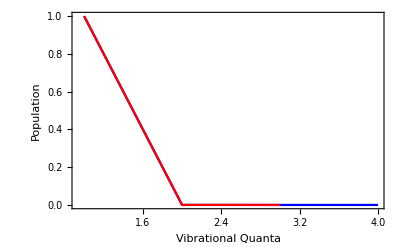

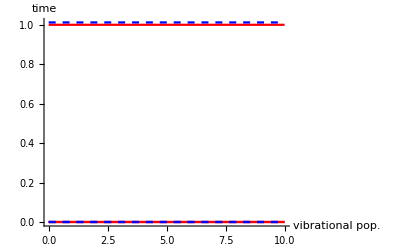

```mathematica
(*to make sure i didn't mess up, let's compare to a Maxwell Boltzmann distribution to if they have agreement*)
Be=.368h 100 c;
ωe=634 100 c 2 π;
vibMaxBoltz[v_,T_]:=(Exp[-ℏ ωe/(2kb T)](1-Exp[-ℏ ωe/(kb T)])^-1)^-1 Exp[-ℏ (ωe(v+1/2))/(kb T)]
MaxBoltz[v_,J_,T_]:=vibMaxBoltz[v,T]((2J+1)Exp[-(Be J(J+1))/(kb T)])/Sum[(2k+1)Exp[-(Be k(k+1))/(kb T)],{k,3/2,jMax}]

(*for comparison of Max-Boltz vibrational populations with model, sum over rotational levels*)
vibLevel=0;
vib1[t_]=Total[Table[Sum[Subscript[n, i,j][t]/.sln,{j,3/2,jMax}],{i,vibLevel,vibLevel}]];
vibLevel=1;
vib2[t_]=Total[Table[Sum[Subscript[n, i,j][t]/.sln,{j,3/2,jMax}],{i,vibLevel,vibLevel}]];
vibLevel=2;
vib3[t_]=Total[Table[Sum[Subscript[n, i,j][t]/.sln,{j,3/2,jMax}],{i,vibLevel,vibLevel}]];
MBVib=Table[Sum[MaxBoltz[i,k,T],{k,3/2,jMax}],{i,0,vMax}];

tProbe=100;

(*this plots the expected vibrational populations for both the model and Max-Boltz predicitons at a time tProbe*)
Show[ListLinePlot[MBVib,PlotRange->All,PlotStyle->Blue,Frame->True,FrameLabel->{"Vibrational Quanta","Population"}],ListLinePlot[Flatten[Table[Sum[Subscript[n, i,j][t]/.sln,{j,3/2,jMax}]/.t->tProbe,{i,0,vMax-1}]],PlotStyle->Red,PlotRange->All]]

(*this plots the expected vibrational populations for both the model and Max-Boltz predicitons at a time tProbe*)
Show[Plot[{vib1[t],vib2[t],vib3[t]},{t,0,10},PlotRange->All,PlotStyle->Red,AxesLabel->{"vibrational pop.","time"}],Plot[{Sum[MaxBoltz[0,k,T],{k,0,100}],Sum[MaxBoltz[2,k,T],{k,0,100}],Sum[MaxBoltz[1,k,T],{k,0,100}]},{t,0,10},PlotStyle->Table[{Blue,Dashed},{i,1,3}]]]

(*looks pretty good*)
```

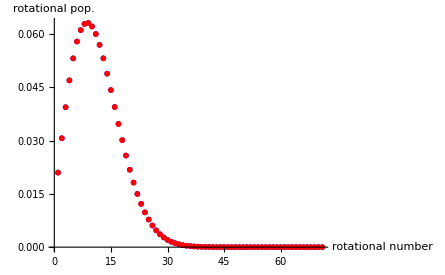

```mathematica
(*Now let's look at rotational level populations*)
tProbe=120000;
rotationalPop=Flatten[Table[Subscript[n, 0,J][t]/.sln/.t->tProbe,{J,3/2,jMax}]];
MBrotPop=Table[MaxBoltz[0,J,T],{J,3/2,jMax}];
ListPlot[{rotationalPop,MBrotPop},AxesLabel->{"rotational number","rotational pop."},PlotStyle->{Blue,{Red,Dashed}},PlotRange->All]

(*okay, it looks in model the molecules aren't equillibrated rotationally, even at 10000 sec. Blackbody spectrum isn't peaked very strongly in the microwave regime so this isn't surprising. But the lack of equillibriation is also partly because I started with crazy initial conditions. If I make it more reasonable, the boltzman distribution should be fine, or I could just wait longer for the populations to redistribute. But I can't propogate my rate equation model past 10000 sec without crashing my computer so I'm going to leave it for now*)
```

{1.}

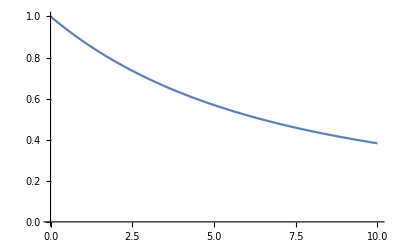

```mathematica
Nn[t_]=Subscript[n, 0,7/2][t]/.sln;
Nn[000]
Plot[Nn[t],{t,0,10},PlotRange->{0,1}]
```

```mathematica
{1.}
```

{1.}

```mathematica
MaxBoltz[0,20,T]
```

0.0237256

```mathematica
rotationalPop
```

{0.0209704,0.030634,0.0393595,0.0469103,0.0531079,0.0578385,0.0610549,0.0627749,0.063075,0.0620818,0.059961,0.0569047,0.0531191,0.0488127,0.0441857,0.0394214,0.0346799,0.0300941,0.0257681,0.021777,0.0181688,0.0149679,0.0121779,0.00978655,0.00776951,0.00609419,0.00472327,0.00361756,0.00273826,0.00204857,0.00151487,0.00110733,0.000800169,0.000571624,0.000403726,0.000281921,0.000194649,0.000132886,0.0000897054,0.000059881,0.0000395277,0.0000258029,0.0000166572,0.0000106344,6.71445×10^-6,4.19279×10^-6,2.58941×10^-6,1.58165×10^-6,9.55519×10^-7,5.70948×10^-7,3.37433×10^-7,1.97251×10^-7,1.1405×10^-7,6.5227×10^-8,3.6899×10^-8,2.06474×10^-8,1.14283×10^-8,6.25708×10^-9,3.38873×10^-9,1.81545×10^-9,9.62086×10^-10,5.0435×10^-10,2.61543×10^-10,1.34168×10^-10,6.80849×10^-11,3.41787×10^-11,1.69732×10^-11,8.33836×10^-12,4.05235×10^-12,1.94825×10^-12,9.26613×10^-13}

```mathematica
TDM[3,0]
```

0.00235